# Tet conv rates

```mathematica
myAxesSize=15;
myLabelSize=12;
myImageSize=500;
```

Case 2 - u(x,y,z) = x^2+y^2+z^2

### Pts extracted from pz

```mathematica
neq={114,840,2754,6432,12450};
h={1,1/2,1/3,1/4,1/5};
h1={0.11514,0.0310188,0.0146744,0.00872461,0.00586929};
l2={0.105454,0.026357,0.0117135,0.00658868,0.00421668};
semih1={0.046225,0.0163547,0.00883921,0.0057191,0.00408267};
ptsh1=Table[{h[[i]],h1[[i]]},{i,Length[neq]}];
ptsl2=Table[{h[[i]],l2[[i]]},{i,Length[neq]}];
ptssemih1=Table[{h[[i]],semih1[[i]]},{i,Length[neq]}];
```

### Plots

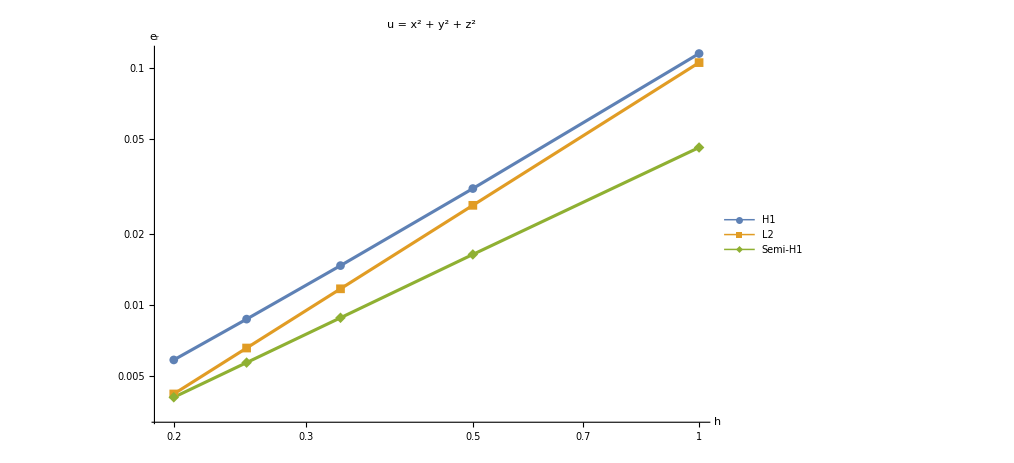

```mathematica
ListLogLogPlot[{ptsh1,ptsl2,ptssemih1},PlotRange->All,PlotStyle->Thickness[0.003],ImageSize->myImageSize 1.5,PlotLabel->Style["u = x^2 + y^2 + z^2",14,Black],AxesLabel->{Style["h",myAxesSize,Black],Style["e_r",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black],Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"H1","L2","Semi-H1"},{0.75,0.85}]]
```

### Conv rates

```mathematica
convratesh1=Range[Length[neq]-1];
convratesl2=Range[Length[neq]-1];
convratesh1semi=Range[Length[neq]-1];
For[i=1,i≤Length[neq]-1,i++,
convratesh1[[i]]=Log[h1[[i]]/h1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesl2[[i]]=Log[l2[[i]]/l2[[i+1]]]/Log[h[[i]]/h[[i+1]]];
convratesh1semi[[i]]=Log[semih1[[i]]/semih1[[i+1]]]/Log[h[[i]]/h[[i+1]]];
]
convratesh1
convratesl2
convratesh1semi
```

{1.89217,1.846,1.8074,1.7765}

{2.00036,2.00015,2.00009,2.00008}

{1.49897,1.51756,1.51343,1.51051}